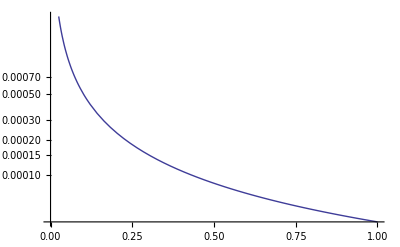

```mathematica
r=256;
c=1.1;
nf[d_]:=(10000*d+0.1)^-c
LogPlot[nf@d/.c->1.2,{d,0,1}]
SeedRandom[1923];
```

```mathematica
noise=RandomComplex[{-1-I,1+I},{r,r}];
fnoise=RandomComplex[{-1-I,1+I},{r,r}];
Export["~/Desktop/fourier.gif",Parallelize@Table[
For[x=1,x≤r,x++,
For[y=1,y≤r,y++,
fnoise[[x,y]]=Re[noise[[x,y]]*nf[((x-0.5)/r-0.5)^2+((y-0.5)/r-0.5)^2]]+Im[noise[[x,y]]*nf[((x-0.5)/r-0.5)^2+((y-0.5)/r-0.5)^2]]*d;
]
];
if=InverseFourier@fnoise;
terrain=ReliefImage[Abs@if,ImageSize->r];
fsplot=ImageAdjust@Image[Log@Abs@fnoise,ImageSize->r];
ct=Graphics@Text[N@c];
Print[N@d];
ImageAssemble[{ImagePad[fsplot,r/4+1,Black],ImageCompose[ImagePad[ImagePad[terrain,1,Yellow],r/4,"Periodic"],ct,{25,10}]}],
{d,0,3,.05}]]
```

0.4

0.

0.05

0.45

0.1

0.15

0.5

0.2

0.25

0.55

0.3

0.6

0.65

0.35

0.7

0.8

0.85

0.75

0.9

1.2

1.25

0.95

1.3

1.

1.05

1.35

1.4

1.1

1.45

1.15

1.5

1.55

1.6

1.65

2.

2.05

1.7

2.1

2.15

1.75

1.8

2.2

2.25

1.85

2.3

1.9

1.95

2.35

2.4

2.45

2.7

2.5

2.55

2.75

2.6

2.8

2.65

2.85

2.9

2.95

3.

~/Desktop/fourier.gif